```mathematica
SetAttributes[tex,HoldFirst]
tex[exp_]:=TeXForm[HoldForm[exp]]
tf:=TableForm
mf:=MatrixForm
```

# Complex Analysis

Complex Numbers

## Algebra

A complex number is a hybrid object with the properties of both a (two dimensional) vector and a number.

Properties of a vector space

Properties of a number field

Complex Plane

Addition

Multiplication

## Conjugate

## Polar Representation

### Conversion Cartesian ⟷ Polar

```mathematica
CoordinateTransformData["Cartesian"-> "Polar","Mapping", {x,y}]
```

{√(x^2+y^2),ArcTan[x,y]}

```mathematica
CoordinateTransformData["Polar"->"Cartesian","Mapping", {r,φ}]
```

{r Cos[φ],r Sin[φ]}

## Euler’s Formula

## De Moivre’s Theorem

## n-th Roots of Unity

## Complex Exponent

## Complex Logarithm

Differentiation

## Limits

## Continuity

## Derivatives

## Rules for Differentiation

## Cauchy-Riemann Equations

## Analytic Functions

## Harmonic Functions

Elementary Complex Functions

## Polynomials

## Exponential

## Trigonometric

## Hyperbolic

## Logarithmic

Integration

## Contours in the Complex Plane

## Complex Line Integrals

## Cauchy Integral Theorem

## Cauchy Integral Formulas

Series and Residues

## Sequences and Series

[TODO]: Section ‘Sequences and Series’ --> MMa
[TODO]: Section ‘Sequences and Series’ --> LATEX / GitHub
Complex Series
  Convergent Series
    Def. Sequence
    Def. Series
    Theorem 1.1 Null Test
    Corollary Thm 1.1 Non-Null Test
  Basic Series
    Thm 1.2 Geometric Series
    Thm 1.3 Series n^(-p)
  Convergence Theorems
    Thm 1.4 Sum/Product Rule
    Thm 1.5 Re / Im Series
    Thm 1.6 Comparison Test
  Absolute Convergence
    Def. Absolutely Convergent
    Thm 1.7 Absolute Convergence Test
    Thm 1.8 Triangle Inequality
    Thm 1.9 Ratio Test

### Convergent Series

### Basic Series

### Convergence Theorems

### Absolute Convergence

## Power Series

### Radius of Convergence

### Disc of Convergence

### Differentiation of Power Series

## Taylor Series

### Example

```mathematica
Series[5/(3+7z),{z,0,5}]//Normal
```

5/3-(35 z)/9+(245 z^2)/27-(1715 z^3)/81+(12005 z^4)/243-(84035 z^5)/729

```mathematica
Series[5/7 1/(3/7+z),{z,0,5}]
```

5/3-(35 z)/9+(245 z^2)/27-(1715 z^3)/81+(12005 z^4)/243-(84035 z^5)/729+O[z]^6

```mathematica
Table[5/7(-1)^k z^k/(3/7)^(k+1),{k,0,5}]
```

{5/3,-(35 z)/9,(245 z^2)/27,-(1715 z^3)/81,(12005 z^4)/243,-(84035 z^5)/729}

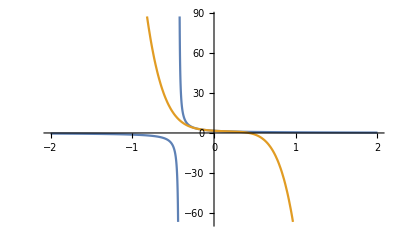

```mathematica
Plot[{5/7 1/(3/7+z),5/3-(35 z)/9+(245 z^2)/27-(1715 z^3)/81+(12005 z^4)/243-(84035 z^5)/729},{z,-2,2}]
```

```mathematica
ComplexPlot3D[5/3-(35 z)/9+(245 z^2)/27-(1715 z^3)/81+(12005 z^4)/243-(84035 z^5)/729,{z,-2-2I,2+2I}]
```

-Graphics3D-

```mathematica
ComplexPlot3D[5/7 1/(3/7+z),{z,-2-2I,2+2I}]
```

-Graphics3D-

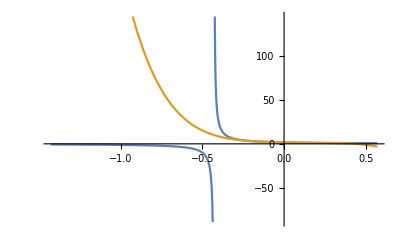

```mathematica
Plot[{5/7 1/(3/7+z),5/3-(35 z)/9+(245 z^2)/27-(1715 z^3)/81+(12005 z^4)/243-(84035 z^5)/729},{z,-10/7,4/7}]
```

```mathematica
?SumConvergence
```

### Cauchy-Hadamard Formula

Add text here ... HOW-TO typeset?

#### Strategy

```mathematica
SeriesCoefficient[-Log[1-z^2],{z,0,n}]
```

Piecewise[{{(1+(-1)^n)/n, n>0}, {0, True}}]

```mathematica
GeneratingFunction[(1+(-1)^(n+1))/(n+1),n,z]
```

-Log[1-z]/z-Log[1+z]/z

```mathematica
MaxLimit[1/Abs[(1+(-1)^(n+1))/(n+1)]^(1/n),n->Infinity]
```

1

```mathematica
ComplexPlot3D[-Log[1-z]/z-Log[1+z]/z,{z,-5-2π ⅈ,5+2π ⅈ}]
```

-Graphics3D-

## Laurent Series

## Zeros and Singularities

## Residues

## Residue Theorem

Temp

## Tmp-1

```mathematica
f[y_,n_]:=D[Cosh[x],{x,n}]/.x:>y
```

```mathematica
f[a,1]
```

Sinh[a]

## Tmp-2

```mathematica
ClearAll[m1,m2,m3];
m1:=({{1, 0, -3}, {0, 1, -1}, {0, 0, 1}});
m2[ϕ_]:=({{Cos[ϕ], Sin[ϕ], 0}, {Sin[ϕ], Cos[ϕ], 0}, {0, 0, 1}});
m3:=({{1, 0, 3}, {0, 1, 1}, {0, 0, 1}});
```

```mathematica
m3.m2[π].m1.{5,1,1}
```

{1,1,1}

```mathematica
ClearAll[m1,m2,m3];
m1:=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
m2[ϕ_]:=({{Cos[ϕ], Sin[ϕ], 0}, {Sin[ϕ], Cos[ϕ], 0}, {0, 0, 1}});
m3:=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
m3.m2[π/2].m1.{2,0,1}
```

{0,2,1}

```mathematica
m3.m2[π/2].m1//mf
```

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1)

```mathematica
({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).{{2},{0},{1}}//mf
```

(0
2
1)

```mathematica
ClearAll[z,m,α];
z=5+3ⅈ;
m=4+2ⅈ;
m=0;
α=(1+ⅈ)/(√2);
α=(0+ⅈ)/1;
```

```mathematica
ReIm[(z-m)α+m]
```

{-3,5}

## =>Tmp-3: Bouw rc

```mathematica
ClearAll[rc];
rc[f_,{x_,x0_}]:=Reduce[SumConvergence[FullSimplify[SeriesCoefficient[f,{x,x0,n}],n∈Integers&&n≥0] (x-x0)^n,n],Abs[x-x0]]
```

```mathematica
rc[1/(1-z),{z,0}]
```

Abs[z]<1

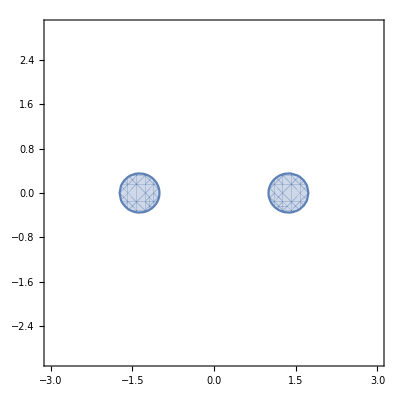

```mathematica
reg=Reduce[Abs[z^2-2]<1,z,Complexes]/.{Re[z]:>x,Im[z]:>y};
RegionPlot[reg,{x,-3,3},{y,-3,3}]
```

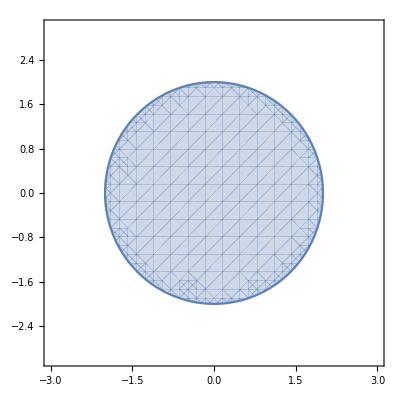

```mathematica
reg=Reduce[Abs[z]<2,z,Complexes]/.{Re[z]:>x,Im[z]:>y};
RegionPlot[reg,{x,-3,3},{y,-3,3}]
```

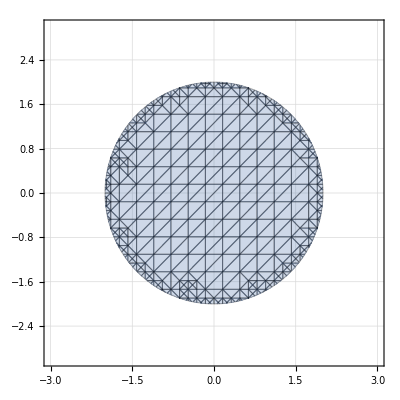

```mathematica
RegionPlot[reg,{x,-3,3},{y,-3,3},Mesh->All,GridLines->Automatic]
```

```mathematica
ClearAll[rc1];
rc1[]:=Module[{},
1]
```

```mathematica
rc1[]
```

1

```mathematica
n∈Integers
```

n∈ℤ

```mathematica
n ∈ Integers
```

n∈ℤ

```mathematica
x=1;
ClearAll[x];
LinearModelFit[RandomReal[1,{10,2}],{1,x},x]
```

FittedModel[0.527982+0.313504 x]

## Tmp-4: Exercises OU M337 B3

### OU B3 Problem 1.1

```mathematica
ClearAll[s1,s2];
s1[n_]:=Sum[(ⅈ/2)^k,{k,0,n}]
s2[n_]:=(1-(ⅈ/2)^(n+1))/(1-ⅈ/2)
```

```mathematica
Table[s1[n],{n,0,3}]//tf
1/(1-1/2 ⅈ)//N
s2[1000]//N
```

1
1+ⅈ/2
3/4+ⅈ/2
3/4+(3 ⅈ)/8

0.8+0.4 ⅈ

0.8+0.4 ⅈ

### OU B3 Problem 1.2a

```mathematica
ClearAll[s1,s2];
s1[n_]:=Sum[(ⅈ/4)^k,{k,1,n}]
s2[n_]:=(ⅈ/4-(ⅈ/4)^(n+1))/(1-ⅈ/4)
```

```mathematica
Table[s1[n],{n,1,3}]//tf
s2[3]
```

ⅈ/4
-1/16+ⅈ/4
-1/16+(15 ⅈ)/64

-1/16+(15 ⅈ)/64

```mathematica
(4-(1/2)^4)/(1/2)
```

63/8

### OU B3 Problem 1.2b

```mathematica
ClearAll[s1,s2];
s1[n_]:=Sum[-7ⅈ(-ⅈ)^k,{k,0,n}]
s2[n_]:=-7ⅈ(1-(-ⅈ)^(n+1))/(1-(-ⅈ))
s1[1000]
s2[1000]
```

-7 ⅈ

-7 ⅈ

### tmp

```mathematica
ClearAll[a,s];
a[n_,{A_,R_}]:=A R^(n-1)
s[n_,{A_,R_}]:=(A-A R^n)/(1-R)
Table[a[k,{1000,0.5}],{k,0,9}]//tf
Table[a[k,{1000,0.5}],{k,1,10}]//Total
s[10,{1000,0.5}]
```

1998.05

1998.05

```mathematica
ClearAll[a,s];
a[n_,{A_,R_}]:=A R^n
s[n_,{A_,R_}]:=(A-A R^(n+1))/(1-R)
Table[a[k,{2,0.5}],{k,1,1}]//tf
Table[a[k,{1,0.5}],{k,0,3}]//Total
```

1.

1.875

## Tmp-5: Tetrahedron

```mathematica
ClearAll[f,g]
f[x_]:=RSolve[{a[n]-a[n-1]-a[n-2]==0,a[1]==1,a[2]==1},a[n],n][[1,1,2]]/.n:>x
```

```mathematica
Table[f[k],{k,1,10}]
```

{1,1,2,3,5,8,13,21,34,55}

```mathematica
?GeneratingFunction
```

```mathematica
GeneratingFunction[n^2,n,z]
```

(-z-z^2)/(-1+z)^3

```mathematica
SeriesCoefficient[(-z-z^2)/((-1+z)^3(1-z)),{z,0,n},Assumptions->{n>=0}]
```

1/6 n (1+3 n+2 n^2)

```mathematica
g[n_]:=1/6 n (1+3 n+2 n^2)
g[5]
```

55

```mathematica
g[n]-g[n-1]
```

-1/6 (1+3 (-1+n)+2 (-1+n)^2) (-1+n)+1/6 n (1+3 n+2 n^2)

```mathematica
RSolve[{a[n]-a[n-1]==-1/6 (1+3 (-1+n)+2 (-1+n)^2) (-1+n)+1/6 n (1+3 n+2 n^2),a[1]==1},a[n],n]
```

{{a[n]→1/6 (1+n) (n+2 n^2)}}